# Sustained release & replenishment at mature PF synapses

#### Based on models in Sakaba, Neuron, 2008 and Dousseau et al., eLife, 2017

Description : 
Lokal Ca ~75 µM = Ca from 1 P/Q @ 10 nm and cluster of 5 N @ 40 nm approximated by Gaussians (Erf + Exp would also be possible but calculations take longer); file Local Ca fit and pv.nb (can be provided upon request)
Residual global Ca (6 PQ + 5 N, volume averaged) in the absence of dye approximated by bi-exp function; contribution of PQ and N can be weighted to better reproduce blocker results; file Global Ca fit.nb (can be provided upon request)
pv ~0.65 (for 6 mM extracellular Ca)

## Edit

```mathematica
NBlock=0;
PQBlock=0;
(*PQcorr=0.7;*)  (*max 1.3; changes the contribution of PQ and N to global Ca*)

Rec=0;
APN=49;   (*CAVE: 0 = 1 AP due to start of summation at t0*)
ISI=50*10^-3;

t0=0.0009;
t1=0.01;

RSt=t0+APN*ISI+0.05;
CaRest=250*10^-9;

(*Full recovery table*)
(*RecTab={RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17,RSt+5.17,RSt+10.17,,RSt+20.17};*)

(*If[Rec==1,
RecTab={RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3};
SubTab={RSt,RSt+70*^-3,RSt+170*^-3,RSt+370*^-3};
]*)

(*If[Rec==1,
RecTab={RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17};
SubTab={RSt,RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17};
]*)

(*If[Rec==1,
RecTab={RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17,RSt+5.17};
SubTab={RSt,RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17};
]*)

If[Rec==1,
RecTab={RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17,RSt+5.17,RSt+10.17};
SubTab={RSt,RSt+70*^-3,RSt+170*^-3,RSt+370*^-3,RSt+670*^-3,RSt+1.17,RSt+2.17,RSt+5.17};
]

If[Rec==1,
TimeWindow=t0+Last[RecTab]+0.5,
TimeWindow=RSt
];
If[APN≤1,
TimeWindow=t1];
```

## Calcium

### Lokal Calcium signal

```mathematica
Clear[Cai,CaiRec,CaiAll]

(*t0=0.0007;
tmax=0.14*10^-3;
amp=200*10^-6;*)

width=0.21*10^-3;

If[NBlock==PQBlock==0,
a1=76*10^-6        (*1PQ @ 10nm+2-3N @ 24 nm  // 76*10^-6 for 1 PQ + 5N @ 40 nm*)
] ;

If[NBlock==1,
a1=62*10^-6         (*1PQ; eigentlich 55*10^-6*)
] ;

If[PQBlock==1,
a1=21*10^-6  (*2-3N  or 5N*)
] ;

r1=6500;
r2=6500;


(*Cai=Sum[UnitStep[t](a1*(1+Erf[r1*(t-i)])*Exp[-r2*(t-i)]),{i,t0,t0+APN*ISI,ISI}];

If[Rec==1,
CaiRec=Sum[UnitStep[t](a1*(1+Erf[r1*(t-i)])*Exp[-r2*(t-i)]),{i,RecTab}]
];*)

Cai=Sum[a1 * ⅇ^(-((t-i)/width)^2) ,{i,t0,t0+APN*ISI,ISI}];

If[Rec==1,
CaiRec=Sum[a1 * ⅇ^(-((t-i)/width)^2) ,{i,RecTab}]
];

(*Cai=Sum[UnitStep[t-i]amp*(t-i)/tmax*Exp[-(t-i)/tmax],{i,t0,t0+APN*ISI,ISI}];

If[Rec==1,
CaiRec=Sum[UnitStep[t-i]amp*(t-i)/tmax*Exp[-(t-i)/tmax] ,{i,RecTab}]

];*)

If[Rec==1,
CaiAll=Cai+CaiRec+CaRest,
CaiAll=Cai+CaRest
];
```

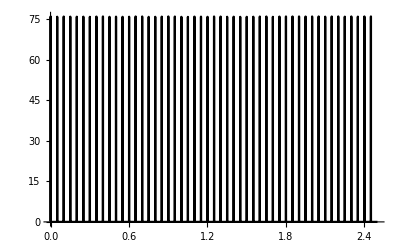

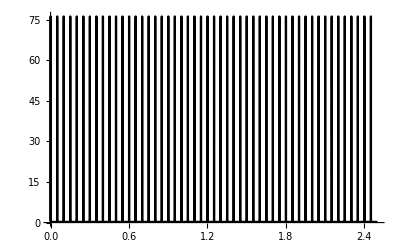

```mathematica
plCai=Plot[10^6 Cai,{t,0,RSt},PlotRange->All,PlotStyle->Black,PlotPoints->2000]
plCaiAll=Plot[10^6 CaiAll,{t,0,TimeWindow},PlotRange->All,PlotStyle->Black,PlotPoints->10000]
```

### Residual = global volume averaged calcium

```mathematica
(*Estimated according to volume averaged Ca from Ca model in the absence of buffer*)

taudf=3.5*10^-3;
tauds=200*10^-3;

(*6PQ+2N*)
If[NBlock==PQBlock==0,
AmpT=3.*10^-6          (*6PQ+2-3N 3. - 3.2 *10^-6// 6PQ+5N 3.7*10^-6*)
];
If[NBlock==PQBlock==0,
Amp2=0.23*10^-6     
];

If[NBlock==1,
 AmpT=2.4*10^-6   (*6 PQ*)
];
If[NBlock==1,
 Amp2=0.2*10^-6 
];

If[PQBlock==1,
AmpT=0.52*10^-6      (*2-3 N 0.52-0.8*10^-6*)
];
If[PQBlock==1,
Amp2=0.055*10^-6       (*0.055-0.07*10^-6*)
];

(*6PQ+5N*)
(*If[NBlock==PQBlock==0,
AmpT=3.7*10^-6          (*6PQ+2N // 6PQ+5N 3.7*10^-6*)
];
If[NBlock==PQBlock==0,
Amp2=0.28*10^-6      (*0.5 before*)
];

If[NBlock==1,
 AmpT=(2.4+PQcorr)*10^-6
];
If[NBlock==1,
 Amp2=0.2*10^-6 
];

If[PQBlock==1,
AmpT=(1.3-PQcorr)*10^-6
];
If[PQBlock==1,
Amp2=0.11*10^-6  
];*)

(*Alternative Caires with tripel exp; including taur*)
(*Caires=Sum[UnitStep[t-i]*(((AmpT-Amp2) Exp[-(t-i)/taudf]+ Amp2 Exp[-(t-i)/tauds])-AmpT Exp[-(t-i)/taur]),{i,t0g,t0+APN*ISI,ISI}];*)

Caires=Sum[UnitStep[t-i]*((AmpT-Amp2) Exp[-(t-i)/taudf]+ Amp2 Exp[-(t-i)/tauds]),{i,t0,t0+APN*ISI,ISI}];

If[Rec==1,
CairesRec=Sum[UnitStep[t-i]*((AmpT-Amp2) Exp[-(t-i)/taudf]+ Amp2 Exp[-(t-i)/tauds]),{i,RecTab}]
];

If[Rec==1,
CairesAll=Caires+CairesRec+CaRest,
 CairesAll=Caires+CaRest
];
```

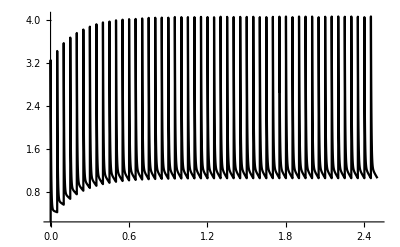

```mathematica
If[Rec==1,
Plot[10^6 CairesAll,{t,0,TimeWindow},PlotRange->All,PlotStyle->Black,PlotPoints->5000,Exclusions->None],
Plot[10^6 CairesAll,{t,0,RSt},PlotRange->All,PlotStyle->Black,PlotPoints->2000,Exclusions->None]
]
```

## Release

```mathematica
Sakaba=1;
Schnegg=0;


(*For adjusting backward rate constants*)

(*CaRest=0*10^-9;
CaiAll=CairesAll=CaRest; 
TimeWindow=0.5;*)

(*For an intrinsic fascilitation mechanism*)
(*gfasc=Piecewise[{{1,t<(ISI)},{5,(ISI)≤t≤RSt+t2},{1,t>RSt+t2}}];*)
gfasc=1;
(*kOnFasc=Piecewise[{{1,t<(ISI)},{5,(ISI)≤t≤RSt+t2},{1,t>RSt+t2}}];*)
kOnFasc=1;

(*If[kOffFasc==1,
kOffFasc=Piecewise[{{1,t<(ISI)},{5,(ISI)≤t≤RSt+t2},{1,t>RSt+t2}}],
kOffFasc=1
];*)
kOffFasc=1;

tau=100*10^-3;
tau2=110*10^-3; (*350*)
amp=17;

(*For pv*)
If[Rec==1,
k2bfac=Piecewise[{{1,t≤RSt},{1+UnitStep[t-(RSt)] *amp*(1- Exp[-(t-RSt)/tau]),RecTab[[2]]≥t>RSt},{1+UnitStep[t-(RecTab[[2]])] *amp*(Exp[-(t-RecTab[[2]])/tau2]),RecTab[[2]]<t}}]
,
k2bfac=1
];

(*For amplitudes*)
(*If[Rec==1,
k2bfac=Piecewise[{{1,t≤RecTab[[1]]},{1+UnitStep[t-RecTab[[1]]] *amp*(1- Exp[-(t-RecTab[[1]])/tau]),RecTab[[2]]≥t>RecTab[[1]]},{1+UnitStep[t-(RecTab[[2]])] *amp*(Exp[-(t-RecTab[[2]])/tau2]),RecTab[[2]]<t}}]
,
k2bfac=1
];*)

(*k2bfac=Piecewise[{{k2/k2b+1,t≤t0},{1,0<t≤RSt},{1+UnitStep[t-(RSt)] *400*(1- Exp[-(t-RSt)/tau]),RecTab[[2]]≥t>RSt},{1+UnitStep[t-(RecTab[[2]])] *400*(Exp[-(t-RecTab[[2]])/tau2]),RecTab[[2]]<t}}];*)

(*For peak RR*)
(*tau=100*10^-3;
tau2=700*10^-3;
k2bfac=Piecewise[{{1,t≤RSt},{1+UnitStep[t-(RSt)] *350*(1- Exp[-(t-RSt)/tau]),RecTab[[3]]≥t>RSt},{1+UnitStep[t-(RecTab[[3]])] *350*(Exp[-(t-RecTab[[3]])/tau2]),RecTab[[3]]<t}}];*)

(*k2bfac=1;*)

RP=2.;
RRP=1;



(*Sakaba with Ca-dependent and -independent rates*)

(*k1=0.45;   (*0.4;0.45; Ca-independent repl of RP*)
k2=8.2;  (*8.7; 8.2;  Ca-independent RP->RRP*)*)
taur1=10;
taur2=5;
k1fac=0.42;
k2fac=8.2;
k1=Piecewise[{{0,t≤t0},{k1fac,t0<t≤RSt},{k1fac*Exp[-t/taur1],t>RSt}}];
k2=Piecewise[{{0,t≤t0},{k2fac,t0<t≤RSt},{k2fac*Exp[-t/taur2],t>RSt}}];

krfac=2.37*10^5;   (*2.25-2.37*10^5 for 2-3 N; factor for Ca-dependent repl of RP*)
k2Cafac=2.7*10^6; (*2.6-2.7*10^6 for 2-3N; factor for Ca-dependent RP->RRP*)

krCa=krfac*CairesAll*Fus'[t];    (*Ca-dependent repl of RP*)
krb=krfac*CaRest; (*RP backward rate*)

k2Ca=k2Cafac*CairesAll;  (*Ca-dependent RP->RRP*)

k2b=k2bfac*RP* k2Cafac*CaRest ;     (* RRP->RP*)
```

### Fix Parameters

```mathematica
If[Sakaba==1,kOffV=3000 ];
If[Sakaba==1,kOnV=9*10^7];                          
If[Sakaba==1,b=0.25];                                          
If[Sakaba==1,g=5000];

If[Schnegg==1,kOffV=9500];
If[Schnegg==1,kOnV=0.9*10^8];
If[Schnegg==1,b=0.25];
If[Schnegg==1,g=6000];
```

```mathematica
Print[kOffV]
Print[kOnV]
Print[b]
Print[g]
```

3000

90000000

0.25

5000

### Sensor model & solving

```mathematica
Fusion=Join[
(* t=0 equations *)
{R1[0]==RP},   (*3*)
{V[0]==RRP},
{CaV[0]==0},
{Ca2V[0]==0},
{Ca3V[0]==0},
{Ca4V[0]==0},
{Ca5V[0]==0},
{Fus[0]==0},

(*x' equations*)

{R1'[t]==-k2*R1[t] -k2Ca*R1[t]+k2b*V[t]+k1+krCa-krb*R1[t]},

{V'[t]==-5*kOnV*kOnFasc*CaiAll* V[t] + kOffFasc*kOffV *CaV[t]+k2*R1[t]+k2Ca*R1[t]-k2b*V[t]},

{CaV'[t]==5*kOnV*kOnFasc*CaiAll* V[t] -kOffFasc*kOffV *CaV[t]-4*kOnV*kOnFasc*CaiAll* CaV[t]+2* b*kOffFasc*kOffV *Ca2V[t]},

{Ca2V'[t]==4*kOnV*kOnFasc*CaiAll* CaV[t] -2* b*kOffFasc*kOffV *Ca2V[t]-3*kOnV*kOnFasc*CaiAll* Ca2V[t] + 3*b^2 *kOffFasc*kOffV *Ca3V[t]},

{Ca3V'[t]==3*kOnV*kOnFasc*CaiAll* Ca2V[t] - 3*b^2 *kOffFasc*kOffV *Ca3V[t]-2*kOnV*kOnFasc*CaiAll* Ca3V[t] + 4*b^3*kOffFasc*kOffV *Ca4V[t]},

{Ca4V'[t]==2*kOnV*kOnFasc*CaiAll* Ca3V[t] - 4*b^3*kOffFasc*kOffV *Ca4V[t]-kOnV*kOnFasc*CaiAll* Ca4V[t] + 5*b^4*kOffFasc*kOffV *Ca5V[t]},

{Ca5V'[t]==kOnV*kOnFasc*CaiAll* Ca4V[t] - 5*b^4*kOffFasc*kOffV *Ca5V[t]-Fus'[t]},

{Fus'[t]==gfasc*g*Ca5V[t]}


(*{R1'[t]==-k2(R1[t]-RP)-k2Ca*(R1[t]-RP)+k2b*V[t]+k1(R1[t]-RP)+krCa-krb},

{V'[t]==-5*kOnV*kOnFasc*CaiAll* V[t] + kOffFasc*kOffV *CaV[t]+k2(R1[t]-RP)+k2Ca*(R1[t]-RP)-k2b*V[t]},

{CaV'[t]==5*kOnV*kOnFasc*CaiAll* V[t] -kOffFasc*kOffV *CaV[t]-4*kOnV*kOnFasc*CaiAll* CaV[t]+2* b*kOffFasc*kOffV *Ca2V[t]},

{Ca2V'[t]==4*kOnV*kOnFasc*CaiAll* CaV[t] -2* b*kOffFasc*kOffV *Ca2V[t]-3*kOnV*kOnFasc*CaiAll* Ca2V[t] + 3*b^2 *kOffFasc*kOffV *Ca3V[t]},

{Ca3V'[t]==3*kOnV*kOnFasc*CaiAll* Ca2V[t] - 3*b^2 *kOffFasc*kOffV *Ca3V[t]-2*kOnV*kOnFasc*CaiAll* Ca3V[t] + 4*b^3*kOffFasc*kOffV *Ca4V[t]},

{Ca4V'[t]==2*kOnV*kOnFasc*CaiAll* Ca3V[t] - 4*b^3*kOffFasc*kOffV *Ca4V[t]-kOnV*kOnFasc*CaiAll* Ca4V[t] + 5*b^4*kOffFasc*kOffV *Ca5V[t]},

{Ca5V'[t]==kOnV*kOnFasc*CaiAll* Ca4V[t] - 5*b^4*kOffFasc*kOffV *Ca5V[t]-Fus'[t]},

{Fus'[t]==gfasc*g*Ca5V[t]}*)


(*{R1'[t]==-k2(R1[t]-RP)-k2Ca*(R1[t]-RP)+k2b*V[t]+k1(RP-R1[t])+krCa-krb},

{V'[t]==-5*kOnV*kOnFasc*CaiAll* V[t] + kOffFasc*kOffV *CaV[t]+k2(R1[t]-RP)+k2Ca*(R1[t]-RP)-k2b*V[t]},

{CaV'[t]==5*kOnV*kOnFasc*CaiAll* V[t] -kOffFasc*kOffV *CaV[t]-4*kOnV*kOnFasc*CaiAll* CaV[t]+2* b*kOffFasc*kOffV *Ca2V[t]},

{Ca2V'[t]==4*kOnV*kOnFasc*CaiAll* CaV[t] -2* b*kOffFasc*kOffV *Ca2V[t]-3*kOnV*kOnFasc*CaiAll* Ca2V[t] + 3*b^2 *kOffFasc*kOffV *Ca3V[t]},

{Ca3V'[t]==3*kOnV*kOnFasc*CaiAll* Ca2V[t] - 3*b^2 *kOffFasc*kOffV *Ca3V[t]-2*kOnV*kOnFasc*CaiAll* Ca3V[t] + 4*b^3*kOffFasc*kOffV *Ca4V[t]},

{Ca4V'[t]==2*kOnV*kOnFasc*CaiAll* Ca3V[t] - 4*b^3*kOffFasc*kOffV *Ca4V[t]-kOnV*kOnFasc*CaiAll* Ca4V[t] + 5*b^4*kOffFasc*kOffV *Ca5V[t]},

{Ca5V'[t]==kOnV*kOnFasc*CaiAll* Ca4V[t] - 5*b^4*kOffFasc*kOffV *Ca5V[t]-Fus'[t]},

{Fus'[t]==gfasc*g*Ca5V[t]}*)


];

Fusion=Flatten[Fusion];

pr1 = NDSolveValue[Fusion,(Fus[t1]),{t,0,t1+ISI},
Method->{"EquationSimplification"->"Residual"}];


If[APN≥2,
prs = NDSolveValue[Fusion,Table[(Fus[i+ISI])-(Fus[i]),{i,ISI,RSt,ISI}],{t,0,RSt+2 ISI},
Method->{"EquationSimplification"->"Residual"}]
];

If[Rec==1,
prrec = NDSolveValue[Fusion,Table[(Fus[i]),{i,RecTab}],{t,0,TimeWindow},
Method->{"EquationSimplification"->"Residual"}]
];

If[Rec==1,
prsub = NDSolveValue[Fusion,Table[(Fus[i]),{i,SubTab}],{t,0,TimeWindow},
Method->{"EquationSimplification"->"Residual"}]
];

If[Rec==1,
prrec=prrec-prsub
];


fussol = NDSolveValue[Fusion,Fus'[t],{t,0,TimeWindow},Method->{"EquationSimplification"->"Residual"}];
Ves=NDSolveValue[{Fusion},V,{t,0,TimeWindow},Method->{"EquationSimplification"->"Residual"}];
RPsol=NDSolveValue[{Fusion},R1,{t,0,TimeWindow},Method->{"EquationSimplification"->"Residual"}];
```

0.656101

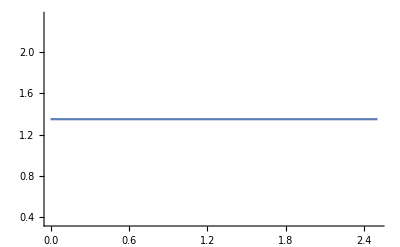

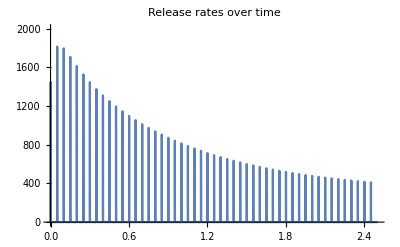

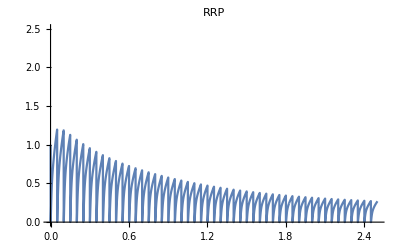

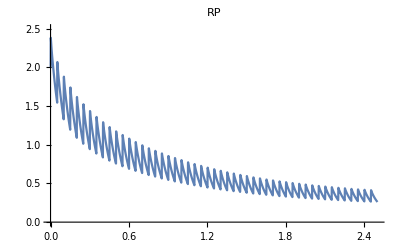

```mathematica
pr1
Plot[k2b,{t,0,TimeWindow},PlotRange->Full]
Plot[fussol,{t,0,TimeWindow},PlotPoints->10000,PlotRange->{Full,{0,2000}},PlotLabel->"Release rates over time"]
Plot[Ves[t],{t,0,TimeWindow},PlotRange->{Full,{0,2.5}},PlotLabel->"RRP",PlotPoints->10000]
Plot[RPsol[t],{t,0,TimeWindow},PlotRange->{Full,{0,2.5}},PlotLabel->"RP"]
```

### pr, PPR, data & plots

```mathematica
(*If[PQBlock==1,pr1*=1.4]*)

If[Rec==1,
prall=Join[{pr1},prs,prrec],
prall=Join[{pr1},prs]
];


PPRs=prall/pr1;

ClearAll[DataPPR]

If[NBlock==PQBlock==0,
DataPPR=Import["/Users/hartmutschmidt/Documents/PF replenishment paper/Mathematica/Base.txt","Table"]
];

If[NBlock==1,
DataPPR=Import["/Users/hartmutschmidt/Documents/PF replenishment paper/Mathematica/CTx.txt","Table"]
];

If[PQBlock==1,
DataPPR=Import["/Users/hartmutschmidt/Documents/PF replenishment paper/Mathematica/AgTx.txt","Table"]
];

DataPPR=Flatten[DataPPR];

If[NBlock==PQBlock==0,
plSim=ListPlot[PPRs,PlotRange->{0,1.5},PlotStyle->{Red,PointSize[Large]}];
plData=ListPlot[DataPPR,PlotRange->{0,1.5},PlotStyle->{Black,PointSize[Large]}]
];

If[NBlock==1,
plSim=ListPlot[PPRs,PlotRange->{0,1.7},PlotStyle->{Red,PointSize[Large]}];
plData=ListPlot[DataPPR,PlotRange->{0,1.7},PlotStyle->{Green,PointSize[Large]}]
];

If[PQBlock==1,
plSim=ListPlot[PPRs,PlotRange->{0,2.5},PlotStyle->{Red,PointSize[Large]}];
plData=ListPlot[DataPPR,PlotRange->{0,2.5},PlotStyle->{Orange,PointSize[Large]}]
];

(*Finding peak RRs*)
tab=Table[i,{i,t0,RSt,ISI}];

Quiet[RR1=Table[FindMaxValue[fussol,{t,i}],{i,tab}]];

If[Rec==1,
Quiet[RR1rec=Table[FindMaxValue[fussol,{t,i}],{i,RecTab}]]];
If[Rec==1,
RRT1=Join[RR1,RR1rec]];
If[Rec==1,
PPR1=RRT1/RRT1[[1]],
PPR1=RR1/RR1[[1]]];

plSimA:=ListPlot[PPR1,PlotRange->All,PlotStyle->{PointSize[Large]}]
```

0.656101

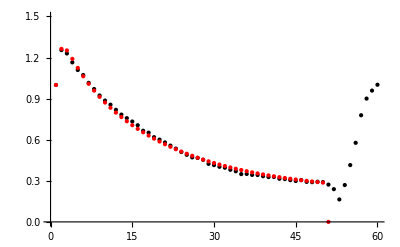

-Graphics-

```mathematica
pr1
Show[plData,plSim]
Show[plData,plSimA]
```

### Time wave and plotting over time

```mathematica
tw=Table[i,{i,0,APN*ISI,ISI}];
If[Rec==1,
tr=RecTab];
If[Rec==1,
tt=Join[tw,tr],
tt=tw];
(*t5AP=Table[i,{i,0,4*ISI,ISI}];*)
If[Rec==0,
DataPPR=DataPPR[[1;;APN+1]],
DataPPR=DataPPR[[1;;APN+1+Length[RecTab]]]
];
Length[tt];
Length[PPRs];
Length[DataPPR];

Sim=Transpose[{tt,PPRs}];
SimA=Transpose[{tt,PPR1}];
Data=Transpose[{tt,DataPPR}];

If[NBlock==PQBlock==0,
plData2=ListPlot[Data,PlotRange->All,PlotStyle->{Black,PointSize[Large]}];
plSim1=ListLinePlot[Sim,PlotRange->All,PlotStyle->Red];
plSim2=ListPlot[Sim,PlotRange->All,PlotStyle->{Red,PointSize[Large]}]
];

If[NBlock==1,
plData2=ListPlot[Data,PlotRange->All,PlotStyle->{Green,PointSize[Large]}];
plSim1=ListLinePlot[Sim,PlotRange->All,PlotStyle->Red];
plSimA1=ListLinePlot[SimA];
plSim2=ListPlot[Sim,PlotRange->All,PlotStyle->{Red,PointSize[Large]}]
];

If[PQBlock==1,
plData2=ListPlot[Data,PlotRange->All,PlotStyle->{Orange,PointSize[Large]}];
plSim1=ListLinePlot[Sim,PlotRange->All,PlotStyle->Red];
plSimA1=ListLinePlot[SimA];
plSim2=ListPlot[Sim,PlotRange->All,PlotStyle->{Red,PointSize[Large]}]
];
```